## Crystal Field Hamiltonian for metal p-, d- and f-shells

© 2013,2019 J. Autschbach, University at Buffalo, SUNY. 

See file LICENSE in https://github.com/jautschbach/mathematica-notebooks for license information and disclaimers.

If you use this notebook for research, please cite these references along with the download link on the author’s web page:

[1] Alessandri, R.; Zulfikri, H.; Autschbach, J.; Bolvin, H., ‘Crystal field in rare-earth complexes: From electrostatics to bonding’, Chem. Eur. J. 2018, 24, 5538–5550. 
[2] Gendron, F.; Páez-Hernández, D.; Notter, F.-P.; Pritchard, B.; Bolvin, H.; Autschbach, J., ‘Magnetic properties and electronic structure of neptunylVI complexes: Wavefunctions, orbitals, and crystal-field models’, Chem. Eur. J. 2014, 20, 7994–8011.

Instructions: Inside a notebook ‘cell’ (input lines), use
Shift-Enter
to evaluate the cell. You can also select a group of cells by clicking on the blue grouping brackets on the right 
and evaluate all cells by Shift-Enter.
Calculate everything from top to bottom via the menu: Evaluation → Evaluate Notebook.
If prompted, allow the evaluation of all Initialization Cells.
Required User Input is indicated in Red.

Make a subdirectory named “exports” where this notebook is stored. There is some LATEX code saved in there. 

If a section is folded (only header visible), double click the blue brackets on the right that have a down-arrow, to un-fold.

### Definitions, Packages (section may be kept folded. allow evaluation of initialization cells when prompted)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
myBlue = RGBColor[0,51/255,153/255];
myOrange=RGBColor[1.0,0.588,0.]  (*Same as #FF9600 used in adf GUI*);
myGreen=ColorData["WebSafe"]["#669900"];
myPurple=ColorData["WebSafe"]["#6633CC"];
myRed = ColorData["HTML"]["FireBrick"];
myPlotStyle = {{myBlue,Thick},{myOrange,Thick},{myGreen,Thick},{myRed,Thick},{myPurple,Thick}, {Black,Thick},{Black,Thick,Dashed}};
```

```mathematica
x/:NumberQ[x]=True;
y/:NumberQ[y]=True;
z/:NumberQ[z]=True;
Bx/:NumberQ[Bx]=True;
By/:NumberQ[By]=True;
Bz/:NumberQ[Bz]=True;
```

Angular momentum operators:
Some of  the code below is from the book Quantum Methods with Mathematica by James M. Feagin (Springer, 1994. I used the 1995 German translation) and has been adapted and extended for the purpose of the calculations done by this notebook.

```mathematica
protected = Unprotect[NonCommutativeMultiply];
A_ ** (B_ + C_) := A ** B + A ** C
(B_ + C_) ** A_ := B ** A + C ** A

A_ ** c_?NumberQ := c A
c_?NumberQ ** A_  := c A
A_ ** (B_ c_?NumberQ):= c A ** B
(A_ c_?NumberQ) ** B_ := c A ** B

A_ ** (B_ c_Rational) := c A ** B
(A_ c_Rational) ** B_ := c A ** B

A_ ** (B_ c_Power):= c A ** B
(A_ c_Power) ** B_:= c A ** B
Protect[ Release[protected] ] ;
```

General angular momentum operators j, jz = j0: Define the result of action of j^2(i) and j_z(i) on a product basis (excluding factors of h-bar) of two angular momenta (i = 1 or 2). "**" identifies a non-commuting 'multiplication' (i.e. the action of an operator). "1" and "2"  identify different angular momenta, such as an electron and a nucleus, two different electrons, two different nuclei, or two different angular momenta such as orbital and spin of the same electron. Here we use it for the latter case.

Notation:
jop[i,m] is the m = -1,0,1 component of the spherical operator set according to l=1 for angular momentum i = 1 or 2 (first or second)
jcomp[i,m,u] is component u = 1,2,3 for x,y,z of the angular momentum operator for angmom.
jsq[i] is the angular momentum square operator

```mathematica
ket::usage ="ket implements multiplication and operator rules for product eigenfunctions of two angular momenta |j1, mj1, j2, mj2⟩.
The definitions also include matrix elements with a corresponding bra.
In this notebook, the first angular momentum is L, and the second is S.";
ket/:jop[1,0]** ket[j1_,j2_,{m1_,m2_}]:= m1 ket[j1,j2,{m1,m2}]
ket/:jop[2,0]** ket[j1_,j2_,{m1_,m2_}]:= m2 ket[j1,j2,{m1,m2}]
ket/:jsq[1]**ket[j1_,j2_,{m1_,m2_}]:=j1(j1+1) ket[j1,j2,{m1,m2}]
ket/:jsq[2]**ket[j1_,j2_,{m1_,m2_}]:=j2(j2+1) ket[j1,j2,{m1,m2}]
```

The following contains the definition of the l=1 set of spherical operators for m = +/- 1. These are closely related to the usual raising and lowering operators.

```mathematica
(* Spin 1 *)
ket/:jop[1,1]**ket[j1_,j2_,{m1_,m2_}]:= 
   -1/(√2)Sqrt[(j1-m1)(j1+m1+1)] ket[j1,j2,{m1+1,m2}]
ket/:jop[1,-1]**ket[j1_,j2_,{m1_,m2_}]:= 
    1/(√2)Sqrt[(j1+m1)(j1-m1+1)] ket[j1,j2,{m1-1,m2}]

(* Spin 2 *)
ket/:jop[2,1]**ket[j1_,j2_,{m1_,m2_}]:= 
   -1/(√2) Sqrt[(j2-m2)(j2+m2+1)] ket[j1,j2,{m1,m2+1}]
ket/:jop[2,-1]**ket[j1_,j2_,{m1_,m2_}]:= 
    1/(√2) Sqrt[(j2+m2)(j2-m2+1)] ket[j1,j2,{m1,m2-1}]
```

Using the spherical operators, define the action of the x,y,z, components (using 1,2,3 for x,y,z)

```mathematica
(* Spin 1 *)
ket/:jcomp[1,1]**ket[j1_,j2_,{m1_,m2_}]:= 
   -1/(√2)jop[1,1] ** ket[j1,j2,{m1,m2}] +1/(√2)jop[1,-1] ** ket[j1,j2,{m1,m2}] ;
ket/:jcomp[1,2]**ket[j1_,j2_,{m1_,m2_}]:= 
    ⅈ/(√2)jop[1,1] ** ket[j1,j2,{m1,m2}] +ⅈ/(√2)jop[1,-1] ** ket[j1,j2,{m1,m2}] ;
ket/:jcomp[1,3]**ket[j1_,j2_,{m1_,m2_}]:= jop[1,0] ** ket[j1,j2,{m1,m2}] ;

(* Spin 2 *)
ket/:jcomp[2,1]**ket[j1_,j2_,{m1_,m2_}]:= 
   -1/(√2)jop[2,1] ** ket[j1,j2,{m1,m2}] +1/(√2)jop[2,-1] ** ket[j1,j2,{m1,m2}] ;
ket/:jcomp[2,2]**ket[j1_,j2_,{m1_,m2_}]:= 
    ⅈ/(√2)jop[2,1] ** ket[j1,j2,{m1,m2}] +ⅈ/(√2)jop[2,-1] ** ket[j1,j2,{m1,m2}] ;
ket/:jcomp[2,3]**ket[j1_,j2_,{m1_,m2_}]:= jop[2,0] ** ket[j1,j2,{m1,m2}] ;
```

We also need a time - reversal operator K = -2 ⅈ jcomp[2,2] K0 where K0 is a complex conjugation operator. In a basis of functions Ylm, that operator K0 changes m to -m (with the added complexity that in Mathematica I need a factor of (-1)^m also (which comes from the Condon-Shortley phase included in the Mathematica definition of spherical harmonics for m>0).
When using operator matrices, one needs to take into consideration that the K0 operator conjugates not only the basis set but also the coefficients of the functions in the Ket set.

```mathematica
ket/: k0op ** ket[j1_,j2_,{m1_,m2_}]:= (-1)^m1 ket[j1,j2,{-m1,m2}]; 
ket/: kop ** ket[j1_,j2_,{m1_,m2_}]:= 
   -2 ⅈ  jcomp[2,2] ** k0op ** ket[j1,j2,{m1,m2}];
```

Normalizion of the functions. KD is here a Kronecker Delta as defined in the Feagin book:

```mathematica
KD[n_,n_] := 1   
KD[n_?NumberQ, m_?NumberQ] := 0
KD[n_ + k_,n_] := 0    
KD[n_,n_ + k_] := 0    
ket/: bra[j1_,j2_,{m1p_,m2p_}]**ket[j1_,j2_,{m1_,m2_}] :=
				 	KD[m1p,m1] KD[m2p,m2] 
ket/: bra[j1_,j2_,{m1p_,m2p_}]**ket[j1_,j2_,{m1_,m2_}] :=
				 	KD[m1p,m1] KD[m2p,m2]
```

Variable transformation rules, Integrations and such (an older version of this notebook used angular integrations explicitly, but it turned out to bee too slow):

```mathematica
Clear[x,y,z, r, θ,φ];
cart2sph := {x :>  r Sin[θ] Cos[φ], y :>  r Sin[θ] Sin[φ], z :> r Cos[θ]} ;
sph2cart := {r :> Sqrt[x^2 + y^2 + z^2]};
sphint[f_] :=Integrate[f Sin[θ],{θ,0,Pi},{φ,0,2 Pi} ](* angular integral*)
```

Overlap integrals of products of x^p y^q z^s calculated by integration over angular coordinates:
the array xyzbas is defined globally, and so are the variables x,y,z

```mathematica
Clear[overlap];
overlap[i_,j_] := Module[
{f,ex,ey,ez,er,
ect,est,ecp,esp,
it1, it2,
ip1,ip2,ip3,ip4,
a, b,sign,
sincosint, res},

(* The following code implements the integral of Sin^a Cos^b
in the interval [0,Pi/2].
We use replacement rules for Sin, Cos in the remaining integration intervals, with the same code, to get the full integrations *) 

sincosint[a_,b_] := Which[
a>1 && b > 1, (1/2)Beta[(a+1)/2,(b+1)/2],
a≥ 1 && b ==  1,1/(1+a) ,
a== 1 && b ≥  1,1/(1+b) ,
a≥ 1 && b ==  0,  2^(a-1) Beta[(a+1)/2,(a+1)/2],
a== 0 && b ≥ 1,  2^(b-1) Beta[(b+1)/2,(b+1)/2],
a == 0 && b == 0, Pi/2,
True, Indeterminate
];

f= xyzbas[[i]]xyzbas[[j]] ;

(* exponents of x, y, z, in the product function *)
ex = Exponent[ x f, x] -1;
ey = Exponent[ y f, y] -1;
ez = Exponent[ z f, z] -1;

(* Print[ToString[cx]<>" "<>ToString[cy]<> " "<>ToString[cz]] ; *)

(* exponents of r, sin(theta), cos(theta), sin(phi), cos(phi) 
in the product function *)
er = ex+ey+ez;
est = ex + ey +1;
ect = ez;
ecp = ex;
esp = ey;

a = est; b = ect; 
it1 = sincosint[a,b];

a = ect; b = est; sign = (-1)^a;
it2 = sign * sincosint[a,b];

a = esp; b = ecp; 
ip1 = sincosint[a,b];

a = ecp; b = esp; sign = (-1)^a ;
ip2 = sign * sincosint[a,b];

a = esp; b = ecp; sign = (-1)^a * (-1)^b;
ip3 = sign * sincosint[a,b];

a = ecp; b = esp; sign = (-1)^b;
ip4 = sign * sincosint[a,b];

res = r^er * (it1 + it2) * (ip1 + ip2 + ip3 + ip4);
Return[res];
];
overlap::usage = "overlap[i,j] gives the integral over the angle coordinates of the product of Cartesian basis functions i,j defined in array xyzbas, after transformation to spherical polar coordinates";
```

The product of two spherical harmonics gives a linear combination of spherical harmonics . The code below is adapted for this task.

```mathematica
coeffCG[l1_,m1_, l2_, m2_,l3_] := 
If[Abs[m1+m2]≤ l3,
(-1)^(m1+m2) √(((2 l1 + 1) ( 2 l2 + 1) ( 2 l3 + 1))/(4 Pi))  ThreeJSymbol[{l1,m1},{l2,m2},{l3,-(m1+m2)}] ThreeJSymbol[{l1,0},{l2,0},{l3,0}] ,0];
coeffCG::usage = "coeffCG gives the Clebsch-Gordan coefficient for the product of two angular momentum eigenfunctions";
```

lprod gives an array of  l,m, and coefficients for the expansion of a product |l1,m1> with |l2,m2>

```mathematica
lprod[l1_,m1_,l2_,m2_] :=
Table[{l3,m1+m2,coeffCG[l1,m1,l2,m2,l3] },{l3,Abs[l1-l2],Abs[l1+l2]}];
lprod::usage = "lprod[l1,m1,l2,m2] returns a table of l,ml values and coefficients of the expansion of the product |l1,m1⟩|l2,m2⟩ in terms of |l,m⟩ functions with l being in the range of Abs[l1-l2] and Abs[l1+l2].";
```

Below is the code to calculate the one-electron CF Hamiltonian given:
1. a basis of |ml, ms> eigenfunctions for a given l-shell (metal shell), as an array of quantum numbers
2. the l-value of the basis
3. the value of s (=1/2 for electrons)
4. the CF Hamiltonian expressed in spherical Harmonics, given as a list of {l,ml, coefficient} sublists
The Hamiltonian is calcukated using the symbolic bra/ket algebra set up above

```mathematica
cfhamiltonian[basis_,l_,s_,pot_] := Module[
{ i,j, k, l1,l2,m1, m2,bl , npot ,cfpot,potop,nop,n, msket,h,t},

npot = Length[pot];
bl = Length[basis];
l2 = l;

h = Table[0,{i,1,bl},{j,1,bl}]; (* initialize hamiltonian matrix *)

Do[ (* loop over bra states in the basis *)
Do[ (* loop over ket states in the basis *)

m2 = basis[[j,1]];
Do[  (* loop over spherical components of the CF operator*)
l1 = pot[[k,1]];
m1 = pot[[k,2]];
cfpot = pot[[k,3]];

(* we let the operator component act on the ket state. If the 
resulting angular momentum in the expansion is not equal to the input l we can drop that term from the list *) 
potop = lprod[l1,m1,l2,m2] // DeleteCases[#,a_/;a[[1]]≠ l] &  ;
nop = Length[potop]; (* numer of terms generated by action of operator on ket *)

Do[
msket={potop[[nop,2]],basis[[j,2]]}; (* we keep the spin of the ket *)
t = cfpot  potop[[nop,3]] (bra[l,s,basis[[i]]] ** ket[l,s,msket]); 
h[[i,j]] = h[[i,j]] + t;
,{n ,1,nop}];

,{k,1,npot}];

,{j,1,bl}];
,{i,1,bl}];
Return[h]
];
cfhamiltonian::usage="cfhamiltonian[basis,l,s,pot] returns the matrix representation of a CF Hamiltonian in an angular momentum eigenfunction basis |l,ml,ms⟩ for s=1/2. The CF potential pot is defined in terms of spherical harmonics as a list of {l,ml,coefficient}.";
```

Construction of a spin - orbit operator matrix in terms of l, s, eigenfunctions, using the ladder operator techniques defined above:

```mathematica
sohamiltonian[basis_,l_,s_]:= Module[{i,j,k,h,bl},
bl = Length[basis];
h =Table[  
∑_(k=-1)^1 ((-1)^k (bra[l,s, basis[[i]]] **  jop[1,k] ** jop[2,-k] **  ket[l,s,basis[[j]]])),{i,1,bl},{j,1,bl}] ;
Return[h];
];
sohamiltonian::usage="sohamiltonian[basis,l,s] returns the matrix representation of the spin-orbit Hamiltonian L dot S in an angular momentum eigenfunction basis |l,ml,ms⟩ for s=1/2.
The Hamiltonian does not include the SO coupling constant ζ";
```

Calculate matrix element of J^2 and Jz for two vectors in a basis set of L,S eigenfunctions  (this is slow; if one needs the whole matrix it is better to generate the basis representation and then transform to another basis):

```mathematica
jmjmatrixelement[basis_,l_,s_,f_,g_]:= Module[{i,k,h,bl,,t1, t2},
bl = Length[basis];
h = {0,0}; (* initialize h *)
t1 = 
∑_(i=1)^bl ∑_(j=1)^bl ((bra[l,s, basis[[i]]] **  
(jsq[1] + jsq[2]  + 2  ∑_(k=-1)^1 ((-1)^k jop[1,k] ** jop[2,-k])) 
**  ket[l,s,basis[[j]]]) Conjugate[f[[i]]] g[[j]] ) ;
t2 =∑_(i=1)^bl ∑_(j=1)^bl ((bra[l,s, basis[[i]]] **  
(jop[1,0] + jop[2,0] ) 
**  ket[l,s,basis[[j]]]) Conjugate[f[[i]]] g[[j]] );
 h = {1/2 (-1+√(1+4 t1)),t2}; 
Return[h];
];
jmjmatrixelement::usage="jmjmatrixelement[basis,l,s,f,g] returns { ⟨f| J^2 |g⟩, ⟨f| J_z |g⟩} where f and g are two functions represented in an angular momentum eigenfunction basis |l,ml,ms⟩ for s=1/2.";
```

Next : code to generate matrix representations of J^2 and Jz in a basis | l, ml, ms⟩

```mathematica
jsqmatrix[basis_,l_,s_]:= Module[{i,k,h,bl},
bl = Length[basis];
h = Table[0,{i,1,bl},{j,1,bl}]; (* initialize h *) 
h = Table[
bra[l,s, basis[[i]]] **  
(jsq[1] + jsq[2]  + 2  ∑_(k=-1)^1 ((-1)^k jop[1,k] ** jop[2,-k])) 
**  ket[l,s,basis[[j]]], {i,1,bl},{j,1,bl}] ;
Return[h];
];
jsqmatrix::usage="jsqmatrix[basis,l,s] returns the matrix representation of (L + S)^2 in an angular momentum eigenfunction basis |l,ml,ms⟩ for s=1/2.";
```

```mathematica
jmmatrix[basis_,l_,s_]:= Module[{i,k,h,bl},
bl = Length[basis];
h = Table[0,{i,1,bl},{j,1,bl}]; (* initialize h *) 
h = Table[
bra[l,s, basis[[i]]] **  
(jop[1,0] + jop[2,0]) 
**  ket[l,s,basis[[j]]], {i,1,bl},{j,1,bl}] ;
Return[h];
];
jmmatrix::usage="jmmatrix[basis,l,s] returns the matrix representation of J_z = (L + S)_z in an angular momentum eigenfunction basis |l,ml,ms⟩ for s=1/2.";
```

For debugging the L or S components, calculate the matrices from the operator components (I checked, it works) :

```mathematica
lsqmatrix[basis_,l_,s_]:= Module[{i,k,h,bl},
bl = Length[basis];
h = Table[0,{i,1,bl},{j,1,bl}]; (* initialize h *)
h = 
Table[
  ∑_(k=1)^3 (bra[l,s, basis[[i]]] ** jcomp[1,k] ** jcomp[1,k] **  ket[l,s,basis[[j]]])
,{i,1,bl},{j,1,bl}] ;
Return[h];
];
ssqmatrix[basis_,l_,s_]:= Module[{i,k,h,bl},
bl = Length[basis];
h = Table[0,{i,1,bl},{j,1,bl}]; (* initialize h *)
h = 
Table[
  ∑_(k=1)^3 (bra[l,s, basis[[i]]] ** jcomp[2,k] ** jcomp[2,k] **  ket[l,s,basis[[j]]])
,{i,1,bl},{j,1,bl}] ;
Return[h];
];
```

Matrices for components of L and S:

```mathematica
lcompmatrix[basis_,l_,s_,u_]:= Module[{i,k,h,bl},
bl = Length[basis];
h = Table[0,{i,1,bl},{j,1,bl}]; (* initialize h *)
h = 
Table[
  (bra[l,s, basis[[i]]] ** jcomp[1,u] **  ket[l,s,basis[[j]]]) 
,{i,1,bl},{j,1,bl}] ;
Return[h];
];
lcompmatrix::usage="lcompmatrix[basis,l,s,u] returns the matrix representation of L_u, u = 1,2,3 for x,y,z in an angular momentum eigenfunction basis |l,ml,ms⟩ for s=1/2.";
```

```mathematica
scompmatrix[basis_,l_,s_,u_]:= Module[{i,k,h,bl},
bl = Length[basis];
h = Table[0,{i,1,bl},{j,1,bl}]; (* initialize h *)
h = 
Table[
  bra[l,s, basis[[i]]] ** jcomp[2,u] **  ket[l,s,basis[[j]]]
,{i,1,bl},{j,1,bl}] ;
Return[h];
];
scompmatrix::usage="scompmatrix[basis,l,s,u] returns the matrix representation of S_u, u = 1,2,3 for x,y,z in an angular momentum eigenfunction basis |l,ml,ms⟩ for s=1/2.";
```

Matrix for the time reversal operator

```mathematica
kopmatrix[basis_,l_,s_]:= Module[{i,k,h,bl},
bl = Length[basis];
h = Table[0,{i,1,bl},{j,1,bl}]; (* initialize h *)
h = 
Table[
  bra[l,s, basis[[i]]] ** kop **  ket[l,s,basis[[j]]]
,{i,1,bl},{j,1,bl}] ;
Return[h];
];
kopmatrix::usage="kopmatrix[basis,l,s] returns the matrix representation of the time reversal operator K in an angular momentum eigenfunction basis |l,ml,ms⟩ for s=1/2. Any action of the complex conjugation part in K on the coefficients of a function represented in this basis needs to be considered separately.";
```

### Set up ligand positions and potential at origin:

User Input: Define a  ligand field by specifying ligand positions relative to the origin.
Use a simple case first where we have axial ligands (parameter b) and 3 equatorial ligands (parameter a). 
For now, we set the equatorial ligands up as a perfect hexagon.

```mathematica
ligandPos = {
{0,0,b},
{0,0,-b},
a  {1,0,0},
a {-1,0,0},
a {0,1,0},
a {0,-1,0}
}; 
n = Length[ligandPos]; (* number of ligands = Length of coordinate list *)
TableForm[ligandPos ,TableHeadings->{Table["L"<>ToString[i],{i,1,n}],{"x","y","z"}}, TableSpacing->{3,3},TableAlignments->Right] (* print list of ligand positions *)
```

| x | y | z
L1 | 0 | 0 | b
L2 | 0 | 0 | -b
L3 | a | 0 | 0
L4 | -a | 0 | 0
L5 | 0 | a | 0
L6 | 0 | -a | 0

```mathematica
Graphics3D[{Red,Thick,Line[Table[{{0,0,0},ligandPos[[i]] /.{a->2,b->1}},{i,1,Length[ligandPos]}]]}]
```

-Graphics3D-

Define the potential energy (in terms of a positive repulsive interaction) at the coordinate origin in terms of inverse distances:

```mathematica
rpot = ∑_(i=1)^n ((x -ligandPos[[i,1]])^2+ (y -ligandPos[[i,2]])^2 + (z -ligandPos[[i,3]])^2)^(-1/2);
```

### Multipole expansion of the Crystal - Field

Expand the CF potential in powers of x, y, z. The highest power needed is 2 times the angular momentum of the shell  that we want to 
consider. This gives a multipole expansion of the potential at the center of that shell. 
The Series[] command of Mathematica, used originally in this code, gets very slow for more complicated potentials and higher orders, so I implemented the naive expression with derivatives, which is fast enough.

User Input : Define angular momentum of the metal shell of interest in the next line (l = 1, 2 or 3 for p, d or f, respectively)

```mathematica
l = 3;
```

Create the multipole expansion :

```mathematica
lm = 2 l; (* max L-value in the expansion. Rerun this if l changed *)
mxexp[α_,β_]:=If[0≤α≤β,1,0];
tmp = 0;
Block[{p,q,s,j,i,r,f,c},
Do[  
f = rpot;
c = If[mxexp[p+q+s,lm]==1, D[D[D[f,{z,s}],{y,q}],{x,p}] /. {x->0, y->0,z->0},0];
tmp = tmp + c   / (p!  q!  s! )  x^p y^q z^s ;
,{p,0,lm},{q,0,lm},{s,0,lm}]];
(* Simplify[# ,{a>0,b>0,c>0}]& // Normal // Expand ; *)
mpot = Sum[x^p y^q z^s Coefficient[x y z tmp, x^(p+1) y^(q+1) z^(s+1)] mxexp[p+q+s,lm],{p,0,lm},{q,0,lm},{s,0,lm}];
```

Define the potential for a given case. The expressions can be rather cumbersome. 
One can simplify the expression here if needed, for instance by setting different parameters equal to each other.
 As an example, if one defines an orthorhombic ligand set with ligand positions +/- a, +/- b, +/- c, a cubic system would be obtained from setting
pot = mpot /. {b->a, c->a}.

```mathematica
pot = mpot  ;
```

### Crystal Field in terms of Spherical harmonics

Now we want to get the CF potential expressed in terms of spherical harmonics.
In principle this is very easy, all we have to do is to calculate the expansion coefficients as follows:
potential(x,y,x) = V(r,θ,φ), i.e. express potential in terms of spherical polar coordinates.
Basis: |Y_l^m(θ,φ)> times powers of r. We're only interested in expanding the angular part of V. 
Write the orthonormal (without r-powers) basis set as |b_i>
Expansion: |V(θ,φ)> = ∑_i |b_i>c_i  with c_i being the expansion coefficient for basis fct. i
Unity operator: ∑_i |b_i><b_i| = 1 ,| 
|V(θ,φ)> = ∑_i |b_i><b_i|V(θ,φ)>    (meaning V = one times V)
Therefore, 
c_i = <b_i|V(θ,φ)>
As it turned out, explicit symbolic angular integrations get *extremely* slow for angular momentum > 2 if we work with the full expansion of the potential. Therefore, we adopt a strategy where we  create a transformation forth and back between a basis set of individual x^p y^q z^s and the basis of spherical harmonics, covering angular momenta up to 2l, and code the results of any integrations explicitly. 
Schlegel and Frisch (1995) gave expressions for transformations between spherical harmonics and Cartesian Gaussian basis functions. We can use that approach here as well in a suitably modified version. I implemented the concept, not their final equation (which is for normalized gaussian functions).

Create basis set list with powers of x, y, z up to the desired order:

```mathematica
xyzbas = Table[x^p y^q z^s  mxexp[p+q+s,lm],{s,0,lm},{q,0,lm},{p,0,lm}]//Flatten // DeleteCases[#, 0]& 
nxyz = Length[xyzbas];
```

{1,x,x^2,x^3,x^4,x^5,x^6,y,x y,x^2 y,x^3 y,x^4 y,x^5 y,y^2,x y^2,x^2 y^2,x^3 y^2,x^4 y^2,y^3,x y^3,x^2 y^3,x^3 y^3,y^4,x y^4,x^2 y^4,y^5,x y^5,y^6,z,x z,x^2 z,x^3 z,x^4 z,x^5 z,y z,x y z,x^2 y z,x^3 y z,x^4 y z,y^2 z,x y^2 z,x^2 y^2 z,x^3 y^2 z,y^3 z,x y^3 z,x^2 y^3 z,y^4 z,x y^4 z,y^5 z,z^2,x z^2,x^2 z^2,x^3 z^2,x^4 z^2,y z^2,x y z^2,x^2 y z^2,x^3 y z^2,y^2 z^2,x y^2 z^2,x^2 y^2 z^2,y^3 z^2,x y^3 z^2,y^4 z^2,z^3,x z^3,x^2 z^3,x^3 z^3,y z^3,x y z^3,x^2 y z^3,y^2 z^3,x y^2 z^3,y^3 z^3,z^4,x z^4,x^2 z^4,y z^4,x y z^4,y^2 z^4,z^5,x z^5,y z^5,z^6}

Write the potential as a vector in this basis: potxyzbas. 
The trick with the xyz multiplication below is because Mathematica cannot extract the coefficient of x^0 from the expression without being told so explicitly.
Only entries with nonzero coefficients are produced in the printout.

```mathematica
potxyzbas = Table[Coefficient [x y z pot,x y z  xyzbas[[i]]],{i,1,nxyz}];
TableForm[Table[{xyzbas[[i]],potxyzbas [[i]]},{i,1,nxyz}] // DeleteCases[#,a_/;a[[2]]===0]&
,TableHeadings->{None,{"function","coefficient"}}, TableSpacing->{1,3},TableAlignments->{{Right,Left}}]
```

function | coefficient
1 | 4/(√(a^2))+2/(√(b^2))
x^2 | 1/2 (2/((a^2)^(3/2))-2/((b^2)^(3/2)))
x^4 | 1/24 ((210 a^4)/((a^2)^(9/2))-144/((a^2)^(5/2))+18/((b^2)^(5/2)))
x^6 | 1/720 ((20790 a^6)/((a^2)^(13/2))-(28350 a^4)/((a^2)^(11/2))+8550/((a^2)^(7/2))-450/((b^2)^(7/2)))
y^2 | 1/2 (2/((a^2)^(3/2))-2/((b^2)^(3/2)))
x^2 y^2 | 1/4 (-48/((a^2)^(5/2))+6/((b^2)^(5/2)))
x^4 y^2 | 1/48 (-(1890 a^4)/((a^2)^(11/2))+1710/((a^2)^(7/2))-90/((b^2)^(7/2)))
y^4 | 1/24 ((210 a^4)/((a^2)^(9/2))-144/((a^2)^(5/2))+18/((b^2)^(5/2)))
x^2 y^4 | 1/48 (-(1890 a^4)/((a^2)^(11/2))+1710/((a^2)^(7/2))-90/((b^2)^(7/2)))
y^6 | 1/720 ((20790 a^6)/((a^2)^(13/2))-(28350 a^4)/((a^2)^(11/2))+8550/((a^2)^(7/2))-450/((b^2)^(7/2)))
z^2 | 1/2 (-4/((a^2)^(3/2))+4/((b^2)^(3/2)))
x^2 z^2 | 1/4 (-18/((a^2)^(5/2))-24/((b^2)^(5/2)))
x^4 z^2 | 1/48 (-(1890 a^4)/((a^2)^(11/2))+1080/((a^2)^(7/2))+540/((b^2)^(7/2)))
y^2 z^2 | 1/4 (-18/((a^2)^(5/2))-24/((b^2)^(5/2)))
x^2 y^2 z^2 | 1/8 (360/((a^2)^(7/2))+180/((b^2)^(7/2)))
y^4 z^2 | 1/48 (-(1890 a^4)/((a^2)^(11/2))+1080/((a^2)^(7/2))+540/((b^2)^(7/2)))
z^4 | 1/24 (36/((a^2)^(5/2))+(210 b^4)/((b^2)^(9/2))-162/((b^2)^(5/2)))
x^2 z^4 | 1/48 (450/((a^2)^(7/2))-(1890 b^4)/((b^2)^(11/2))+1170/((b^2)^(7/2)))
y^2 z^4 | 1/48 (450/((a^2)^(7/2))-(1890 b^4)/((b^2)^(11/2))+1170/((b^2)^(7/2)))
z^6 | 1/720 (-900/((a^2)^(7/2))+(20790 b^6)/((b^2)^(13/2))-(28350 b^4)/((b^2)^(11/2))+9000/((b^2)^(7/2)))

Check that we get the correct potential. Required output = True

```mathematica
tmp = ∑_(i=1)^nxyz (potxyzbas[[i]] xyzbas[[i]]);
tmp == pot
```

True

Create a list of Spherical Harmonics as our basis set. We generate that list, ylmbas, along with an index vector ylmindex that tells us later what the l,m numbers of each basis function are (given as a sub-list of 2 numbers {l,m} in ylmindex). 
nb = numbers of Ylm basis functions

```mathematica
nb = ∑_(i=0)^lm (2 i + 1)
ylmbas = Table[SphericalHarmonicY[l1, m1,θ,φ],
{l1,0,lm}, {m1,-l1,l1}] //Flatten ;
ylmindex = Table[{l1, m1},
{l1,0,lm}, {m1,-l1,l1}] // Flatten[#,1] &  ;
Length[ylmbas]==nb (* check that nb has the right value *)
```

49

True

We need the overlap matrix of two polynomials integrated over angular coordinates after transformation to spherical coords. 
This is the overlap matrix of  our Cartesian product basis, leaving powers of r out of the integrations.
I have implemented the integration results analytically using integrals from Gradshteyn & Ryzhik, 6th Ed.,
because the symbolic integrations in Mathematica (when I wrote this first) were slow for high powers of x, y, z.
The code is in the Definitions cell at the beginning of the notebook.

```mathematica
?overlap
```

```mathematica
xyzov = Table[overlap[i,j],{i,1,nxyz},{j,1,nxyz}] //Simplify;
```

Next, we need the coefficient vector xyz2ylm for a spherical Harmonic in terms of Cartesian products, following the procedure by Schlegel & Frisch. We set up that vector specifically for the two basis sets defined above, Cartesian products and Ylm. 
It is important that we use the exact definition of the Spherical Harmonics as in Mathematica ... after some trial and error, the prescription below appears to be correct (it has been checked explicitly with some examples up to l = 6). The term If[m1>0,(-1)^m1,1] is the Condon-Shortley phase which is apparently included in the Mathematica definition of the Ylm.
The functions ylmcart include factors of r^l, necessarily, otherwise the x,y, substitutions and derivatives won’t work. 
In order to get back to the original basis of spherical harmonics, we divide the expansion coefficients by r^l after they are calculated.

```mathematica
ylmcart = Table[ If[m1>0,(-1)^m1,1]/(1 (*r^l1 *))√(((2 l1 + 1) ( l1 - Abs[m1])!)/(4 π (l1 + Abs[m1])!))(x + Sign[m1] I y)^Abs[m1]  1/((2^l1) l1!)D[(z^2 - r^2)^l1,{z,l1+Abs[m1]}],{l1,0,lm},{m1,-l1,l1}] // Flatten;
```

Check that the function list is precisely the same as r^l Y_l^m 
with Ylm as defined in Mathematica. The check is a bit slow but important. 
Required output = True

```mathematica
tmp = ylmcart //. cart2sph //TrigExpand//Simplify;
tmp2 = Table[ r^l1 SphericalHarmonicY[l1, m1,θ,φ],{l1,0,lm},{m1,-l1,l1}] // Flatten  //ExpToTrig// TrigExpand//Simplify;
tmp == tmp2
(* Table[{tmp[[i]],tmp2[[i]] },{i,1,12}]//TableForm *)
```

True

Now we can calculate the coefficients:
r^l Y_l^m=∑_(p,q,s) C_pqs^lm x^p y^q z^s=f(x,y,z), therefore
C_pqs^lm=1/(p! q! s!)(∂/(∂ x))^p (∂/(∂ y))^q (∂/(∂ z))^s  f(x,y,z)|_(x=y=z=0)
The array xyz2ylm is equal to C_pqs^lm divided by r^l to get back to the original basis of  Y_l^m
Taking derivatives in Mathematica is fast, therefore there is no point in coding the final result, 
we can let the software do the differentiations.

```mathematica
xyz2ylm = Table[0,{j,1,nb},{i,1,nxyz}]; (* initialize array *)
Block[{p,q,s,j,i,r,f,c},
Do[  
p = Exponent[x  xyzbas[[i]],x] -1;
q = Exponent[y  xyzbas[[i]],y] -1;
s = Exponent[z  xyzbas[[i]],z] -1;
f = ylmcart[[j]] //. {r -> Sqrt[x^2 + y^2 + z^2]};
c = D[D[D[f,{z,s}],{y,q}],{x,p}] /. {x->0, y->0,z->0};
xyz2ylm[[j,i]] = c   / (p!  q!  s! r^(p+q+s)) ;
,{i,1,nxyz},{j,1,nb}]]
```

We can now use the matrix to transform the Cartesian overlap matrix to the overlap matrix in the Ylm basis set, which must be a unit matrix for one-center functions. Required output = True

```mathematica
tmp = xyz2ylm.xyzov.(ConjugateTranspose[xyz2ylm] ) //Simplify[#,Assumptions->{r∈ Reals}]&  ;
tmp == IdentityMatrix[nb]
```

True

Therefore, the inverse transformation is ylm2xyz = xyzov.ConjugateTranspose[xyz2ylm]

```mathematica
ylm2xyz = xyzov.ConjugateTranspose[xyz2ylm] // Simplify[#,Assumptions->{r∈ Reals}]&;
```

The row index of ylm2xyz is the index for the Cartesian basis

```mathematica
Length[ylm2xyz] == nxyz
```

True

Main result of this section:
We can now write the potential in terms of spherical harmonics, i.e. as a vector potylmbas  in the basis ylmBasis.
There is a pretty-printed output for the potential indicating the l and m value of the basis along with the coefficient. 
Only entries with nonzero coefficients are printed.

```mathematica
potylmbas = Table[ ∑_(j=1)^nxyz (potxyzbas[[j]] ylm2xyz[[j,i]]),{i,1,nb}] //Simplify;
tmp=Table[{i,ylmindex[[i,1]],ylmindex[[i,2]],potylmbas[[i]]},{i,1,nb}] //DeleteCases[#,a_/;a[[4]]===0]&; 
TableForm[tmp,
TableHeadings->{None,{"Basis fct.","l","m","coeff"}},TableAlignments->{{Right,Right,Right,Left}},TableSpacing->{1,10}]
```

Basis fct. | l | m | coeff
1 | 0 | 0 | 4 (2/(√(a^2))+1/(√(b^2))) √π
7 | 2 | 0 | (4 ((a^2)^(3/2)-(b^2)^(3/2)) √(π/5) r^2)/((a^2)^(3/2) (b^2)^(3/2))
17 | 4 | -4 | (√(a^2) √((35 π)/2) r^4)/(3 a^6)
21 | 4 | 0 | 1/3 ((3 √(a^2))/a^6+(4 √(b^2))/b^6) √π r^4
25 | 4 | 4 | (√(a^2) √((35 π)/2) r^4)/(3 a^6)
39 | 6 | -4 | -(3 √(a^2) √((7 π)/26) r^6)/(2 a^8)
43 | 6 | 0 | ((-5 √(a^2) b^8+8 a^8 √(b^2)) √(π/13) r^6)/(2 a^8 b^8)
47 | 6 | 4 | -(3 √(a^2) √((7 π)/26) r^6)/(2 a^8)

The final test is whether the potential, written in the Ylm basis with the coefficients of the Table above, 
is identical to the potential that we started with.
To prove this, we simply convert the original potential to spherical coordinates via a coordinate substitution rule (straightforward from xyz to spherical), and compare with the expression in terms of spherical harmonics. Both expressions need to be expanded and then simplified by Mathematica in a similar way, otherwise the software doesn’t realize that the expressions are identical.
Required output = True

```mathematica
potSph = (pot //. cart2sph )   //Simplify //TrigExpand;
potTest = ∑_(i=1)^nb (SphericalHarmonicY[ylmindex[[i,1]], ylmindex[[i,2]],θ,φ] potylmbas[[i]])  //ExpToTrig //Simplify // TrigExpand ;
potSph == potTest
```

True

Set up a reduced CF potential potylm where only nonzero coefficients show up in a list {l,m,coef}. We also drop the 0,0 coefficient which makes the expression simpler in the end. Depending on the desired approximations, feel free to drop other terms as well by restricting the upper limit of the Table command below to a value less than “nb”.

```mathematica
nb
```

49

```mathematica
potylm=Table[{ylmindex[[i,1]],ylmindex[[i,2]],potylmbas[[i]]},{i,2,nb}]// DeleteCases[#,a_/;a[[3]]===0] & ; 
tmp = TableForm[potylm ,TableHeadings->{None,{"l","m","coeff"}},TableSpacing->{2,4}]
```

l | m | coeff
2 | 0 | (4 ((a^2)^(3/2)-(b^2)^(3/2)) √(π/5) r^2)/((a^2)^(3/2) (b^2)^(3/2))
4 | -4 | (√(a^2) √((35 π)/2) r^4)/(3 a^6)
4 | 0 | 1/3 ((3 √(a^2))/a^6+(4 √(b^2))/b^6) √π r^4
4 | 4 | (√(a^2) √((35 π)/2) r^4)/(3 a^6)
6 | -4 | -(3 √(a^2) √((7 π)/26) r^6)/(2 a^8)
6 | 0 | ((-5 √(a^2) b^8+8 a^8 √(b^2)) √(π/13) r^6)/(2 a^8 b^8)
6 | 4 | -(3 √(a^2) √((7 π)/26) r^6)/(2 a^8)

“coeff” above is related to the CF B-parameters by an angular integration with the radial function for the metal shell, and probably some
other unit conversion. 
At this point, we can check which B (l, m) crystal field terms contribute for a given arrangement of ligands. 
Without symmetry, all of them contribute.
If there is symmetry, there are usually a many terms that do not contribute. 
Depending on the values for the ligand position and on the radial extent of the metal shell, the magnitude of the parameters may be very different. 
At this stage, we have a possibility to perform the radial integration up-front and check with some numerical values how important the different
B-terms can be. This could be used, for instance, to redefine array potylm with some other symbolic parameters.

Define a normalized radial STO function with exponent β:

```mathematica
rad[l_,β_] := √(1/(2^(-3-2 l) β^(-3-2l) Gamma[3+2 l])) r^l Exp[- β r];
rint[f_] := Integrate[f r^2,{r,0,Infinity},Assumptions->{β ϵ Reals,β > 0}];
rint[rad[l,β]^2]
```

1

Perform the radial integation for potylm:

```mathematica
potylm2 = Table[{potylm[[i,1]],potylm[[i,2]],  rint[ ( rad[l,β]^2  potylm[[i,3]] ) ]},{i,1,Length[potylm]}];
TableForm[potylm2 ,TableHeadings->{None,{"l","m","coeff"}},TableSpacing->{2,4}]
```

l | m | coeff
2 | 0 | (18 (-1/((a^2)^(3/2))+1/((b^2)^(3/2))) √(5 π))/β^2
4 | -4 | (495 √(a^2) √((35 π)/2))/(2 a^6 β^4)
4 | 0 | (495 (3 √(a^2) b^6+4 a^6 √(b^2)) √π)/(2 a^6 b^6 β^4)
4 | 4 | (495 √(a^2) √((35 π)/2))/(2 a^6 β^4)
6 | -4 | -(31185 √(a^2) √((91 π)/2))/(8 a^8 β^6)
6 | 0 | (10395 (-5 √(a^2) b^8+8 a^8 √(b^2)) √(13 π))/(8 a^8 b^8 β^6)
6 | 4 | -(31185 √(a^2) √((91 π)/2))/(8 a^8 β^6)

Suppose my ligand distance parameters are all 4 atomic units, and the radial exponent is 2. We can get a feel for the magnitude of the B-terms. 
There may be sign changes if the parameters are changed, as evident from the analytic expressions

```mathematica
potylm2 /. {a->3., b->4., β->2.}  // TableForm[# ,TableHeadings->{None,{"l","m","coeff"}},TableSpacing->{2,4}] &
```

l | m | coeff
2 | 0 | -0.381883
4 | -4 | 0.472001
4 | 0 | 0.44559
4 | 4 | 0.472001
6 | -4 | -0.332972
6 | 0 | -0.233281
6 | 4 | -0.332972

Based on the considerations, we select here the full set of expansion coefficients or a reduced subset. 
We may also eliminate coefficients based on the nature of specific states that we plan to consider. 
The indices in the list “select” refer to the rows of potylm2 as printed above.

```mathematica
select = Table[i,{i,1,Length[potylm2]}]; (* this selects the full set of coefficients *)
select = {5,6,7} ;  
potylm = Table[{potylm2[[select[[i]],1]],potylm2[[select[[i]],2]],potylm2[[select[[i]],3]]},{i,1,Length[select]}];
TableForm[potylm ,TableHeadings->{None,{"l","m","coeff"}},TableSpacing->{2,4}]
```

l | m | coeff
6 | -4 | -(31185 √(a^2) √((91 π)/2))/(8 a^8 β^6)
6 | 0 | (10395 (-5 √(a^2) b^8+8 a^8 √(b^2)) √(13 π))/(8 a^8 b^8 β^6)
6 | 4 | -(31185 √(a^2) √((91 π)/2))/(8 a^8 β^6)

Essentially, these are independent parameters. Therefore, we can make a replacement here, which makes the parameter substitution later a bit easier:

```mathematica
replace = {Γ (13 π/28) /(5/11) √(14/(13 π)),Δ /  ((5 * 7)/(66 √(13 π))),  Γ (13 π/28) /(5/11) √(14/(13 π)) } ;  
potylm = Table[{potylm[[i,1]],potylm[[i,2]],replace[[i]]},{i,1,Length[replace]}] //Simplify;
TableForm[potylm ,TableHeadings->{None,{"l","m","coeff"}},TableSpacing->{2,4}]
```

l | m | coeff
6 | -4 | 11/10 √((13 π)/14) Γ
6 | 0 | 66/35 √(13 π) Δ
6 | 4 | 11/10 √((13 π)/14) Γ

### Considering the action of SO coupling and the CF Hamiltonian on the basis and on the metal shell

We want to follow the lines of Bolvin' s paper and see if we can come up with some suitable angula- momentum eigenfunction combinations that are adapted to the problem’s symmetry and allow us to calculate magnetic properties. First we need to see how we can set up operators properly, using symbolic operator algebra rather than integrations over spatial variables.
The code used here is defined in Section 1:

```mathematica
?lprod
```

```mathematica
?cfhamiltonian
```

```mathematica
?sohamiltonian
```

Test the lprod code. The summation with parameters 7,3,2,1 should generate the function 'ftest' (obtained from explicitly multiplying two SphericalHarmonicY functions in Mathematica. 
Required output = True 
(different simplification of ftest or tmp may be needed to show the equivalence in Mathematica versions different from 7 or 8)

```mathematica
ftest = -1/(4096 π)15 √21 (686 Cos[t]+451 Cos[3 t]+143 Cos[5 t]) (Cos[2 p]-ⅈ Sin[2 p]) Sin[t]^4  //TrigExpand//Simplify; 
tmp = lprod[7,-3,2,1];
(Sum[tmp[[i,3]] SphericalHarmonicY[tmp[[i,1]],tmp[[i,2]],t,p], {i,1,Length[tmp]}] //ExpToTrig//TrigExpand//Simplify)  == ftest
```

True

#### Set up the basis of L, S eigenfunctions for the metal shell and the CF potential in terms of spherical harmonics quantum numbers and coefficients

Create a basis set of  spin orbitals for the metal shell for given l, with alternating alpha and beta spin functions, all formally specified by quantum number pairs {ml, ms}. 
We can also create alpha spin functuions to keep the notation compact for spin-free operators such as CF by setting 'withspin' to False

```mathematica
withspin = True;
s = 1/2;
If[withspin,
basis = Flatten[Table[{mL,mS},{mL,l,-l,-1},{mS,s,-s,-1}],1], basis = Flatten[Table[{mL,mS},{mL,l,-l,-1}, {mS,s,s}],1]
];
nbas = Length[basis];
TableForm[basis,TableHeadings->{Table[i,{i,1,nbas}],{"m_l","m_s"}},TableAlignments->Right,TableSpacing->{1,4}]
```

| m_l | m_s
1 | 3 | 1/2
2 | 3 | -1/2
3 | 2 | 1/2
4 | 2 | -1/2
5 | 1 | 1/2
6 | 1 | -1/2
7 | 0 | 1/2
8 | 0 | -1/2
9 | -1 | 1/2
10 | -1 | -1/2
11 | -2 | 1/2
12 | -2 | -1/2
13 | -3 | 1/2
14 | -3 | -1/2

#### Calculate the CF Hamiltonian in the |l,ml,ms> basis

Using the results for the Hamiltonian from the previous section.
(as a test, I have verified that I get a unit matrix without putting the operator in).
Print the crystal field Hamiltonian in the | l, s, ml, ms > basis:

```mathematica
lslabels = Table["|"<>ToString[l,FormatType->TraditionalForm]<>","<>ToString[basis[[i,1]],FormatType->TraditionalForm]<>","<>ToString[basis[[i,2]],FormatType->TraditionalForm]<>"⟩",{i,1,nbas}];
```

```mathematica
cfh2 = cfhamiltonian[basis,l,s,potylm] //Simplify //Factor; 
Print["CF Hamiltonian, Angular momentum l = "<>ToString[l]];tmp = cfh2 //TableForm[#,TableHeadings->{lslabels,lslabels} ,TableAlignments->Right, TableSpacing->{0,0}]&
```

CF Hamiltonian, Angular momentum l = 3

| |3,3,1/2⟩ | |3,3,-1/2⟩ | |3,2,1/2⟩ | |3,2,-1/2⟩ | |3,1,1/2⟩ | |3,1,-1/2⟩ | |3,0,1/2⟩ | |3,0,-1/2⟩ | |3,-1,1/2⟩ | |3,-1,-1/2⟩ | |3,-2,1/2⟩ | |3,-2,-1/2⟩ | |3,-3,1/2⟩ | |3,-3,-1/2⟩
|3,3,1/2⟩ | -Δ/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 √(5/3) Γ | 0 | 0 | 0 | 0 | 0
|3,3,-1/2⟩ | 0 | -Δ/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 √(5/3) Γ | 0 | 0 | 0 | 0
|3,2,1/2⟩ | 0 | 0 | (6 Δ)/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γ/2 | 0 | 0 | 0
|3,2,-1/2⟩ | 0 | 0 | 0 | (6 Δ)/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γ/2 | 0 | 0
|3,1,1/2⟩ | 0 | 0 | 0 | 0 | -(15 Δ)/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 √(5/3) Γ | 0
|3,1,-1/2⟩ | 0 | 0 | 0 | 0 | 0 | -(15 Δ)/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 √(5/3) Γ
|3,0,1/2⟩ | 0 | 0 | 0 | 0 | 0 | 0 | (20 Δ)/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
|3,0,-1/2⟩ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (20 Δ)/7 | 0 | 0 | 0 | 0 | 0 | 0
|3,-1,1/2⟩ | -1/4 √(5/3) Γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(15 Δ)/7 | 0 | 0 | 0 | 0 | 0
|3,-1,-1/2⟩ | 0 | -1/4 √(5/3) Γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(15 Δ)/7 | 0 | 0 | 0 | 0
|3,-2,1/2⟩ | 0 | 0 | Γ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (6 Δ)/7 | 0 | 0 | 0
|3,-2,-1/2⟩ | 0 | 0 | 0 | Γ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (6 Δ)/7 | 0 | 0
|3,-3,1/2⟩ | 0 | 0 | 0 | 0 | -1/4 √(5/3) Γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ/7 | 0
|3,-3,-1/2⟩ | 0 | 0 | 0 | 0 | 0 | -1/4 √(5/3) Γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ/7

User Input : The parameters should be defined at the end of the previous section such that this Hamiltonian looks reasonably simple. 
Parameter substitutions later seem to work less well. This may require a bit of a forth and back.

```mathematica
cfunit = "see definitions of Δ, Γ";
```

```mathematica
cfvec = Eigenvectors[cfh2] //Simplify; 
cfeig = Eigenvalues[cfh2] //Simplify ;TableForm[Table[{Subscript["v", ToString[i]],cfeig[[i]]},{i,1,nbas}],TableHeadings->{None,{"eigenvector\n no.","eigenvalue\nunits: "<>ToString[cfunit//TraditionalForm]}},TableAlignments->Right]
```

eigenvector
 no. | eigenvalue
units: see definitions of Δ, Γ
v_1 | -Γ/2+(6 Δ)/7
v_2 | -Γ/2+(6 Δ)/7
v_3 | (20 Δ)/7
v_4 | (20 Δ)/7
v_5 | Γ/2+(6 Δ)/7
v_6 | Γ/2+(6 Δ)/7
v_7 | -(8 Δ)/7-1/4 √((5 Γ^2)/3+16 Δ^2)
v_8 | -(8 Δ)/7-1/4 √((5 Γ^2)/3+16 Δ^2)
v_9 | -(8 Δ)/7-1/4 √((5 Γ^2)/3+16 Δ^2)
v_10 | -(8 Δ)/7-1/4 √((5 Γ^2)/3+16 Δ^2)
v_11 | -(8 Δ)/7+1/4 √((5 Γ^2)/3+16 Δ^2)
v_12 | -(8 Δ)/7+1/4 √((5 Γ^2)/3+16 Δ^2)
v_13 | -(8 Δ)/7+1/4 √((5 Γ^2)/3+16 Δ^2)
v_14 | -(8 Δ)/7+1/4 √((5 Γ^2)/3+16 Δ^2)

Note that the eigenvectors are not automatically normalized.

#### Calculate the SO Hamiltonian in the basis

Now let' s calculate the SO Hamiltonian in the same basis. The operator setup code is in Section 1.
We leave out the SO coupling constant for now, i.e. everything needs to be multiplied by ζ = SO coupling constant

```mathematica
?sohamiltonian
```

```mathematica
soh = sohamiltonian[basis,l,s] //Simplify; 
Print["SO Hamiltonian in units of ζ, Angular momentum l = "<>ToString[l]];
tmp = soh //TableForm[#,TableHeadings->{lslabels,lslabels},TableAlignments->Right,TableSpacing->{0,0}]&
```

SO Hamiltonian in units of ζ, Angular momentum l = 3

| |3,3,1/2⟩ | |3,3,-1/2⟩ | |3,2,1/2⟩ | |3,2,-1/2⟩ | |3,1,1/2⟩ | |3,1,-1/2⟩ | |3,0,1/2⟩ | |3,0,-1/2⟩ | |3,-1,1/2⟩ | |3,-1,-1/2⟩ | |3,-2,1/2⟩ | |3,-2,-1/2⟩ | |3,-3,1/2⟩ | |3,-3,-1/2⟩
|3,3,1/2⟩ | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
|3,3,-1/2⟩ | 0 | -3/2 | √(3/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
|3,2,1/2⟩ | 0 | √(3/2) | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
|3,2,-1/2⟩ | 0 | 0 | 0 | -1 | √(5/2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
|3,1,1/2⟩ | 0 | 0 | 0 | √(5/2) | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
|3,1,-1/2⟩ | 0 | 0 | 0 | 0 | 0 | -1/2 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
|3,0,1/2⟩ | 0 | 0 | 0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
|3,0,-1/2⟩ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √3 | 0 | 0 | 0 | 0 | 0
|3,-1,1/2⟩ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √3 | -1/2 | 0 | 0 | 0 | 0 | 0
|3,-1,-1/2⟩ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | √(5/2) | 0 | 0 | 0
|3,-2,1/2⟩ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(5/2) | -1 | 0 | 0 | 0
|3,-2,-1/2⟩ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | √(3/2) | 0
|3,-3,1/2⟩ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √(3/2) | -3/2 | 0
|3,-3,-1/2⟩ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2

Get the eigenvalues and eigenvectors for the SO Hamiltonian (free ion case):

```mathematica
sovec = Eigenvectors[soh] //Simplify; 
soeig = Eigenvalues[soh] //Simplify ;TableForm[Table[{Subscript["v", ToString[i]],soeig[[i]]},{i,1,nbas}],TableHeadings->{None,{"eigenvector\n no.","eigenvalue"}},TableAlignments->Right]
```

eigenvector
 no. | eigenvalue
v_1 | -2
v_2 | -2
v_3 | -2
v_4 | -2
v_5 | -2
v_6 | -2
v_7 | 3/2
v_8 | 3/2
v_9 | 3/2
v_10 | 3/2
v_11 | 3/2
v_12 | 3/2
v_13 | 3/2
v_14 | 3/2

For an f-shell, we get the expected 6 states for f5/2 and 8 states for f7/2. 
It will be nice to know the j, mj values for the eigenfunctions and sort them accordingly. Let's calculate the list

soveco = Orthogonalize[sovec,Method→GramSchmidt];
jmj = Table[jmjmatrixelement[basis,l,s,soveco[[i]],soveco[[i]]],{i,1,nbas}] ;
jmjlabels = Table["|" <> ToString[jmj[[i, 1]], FormatType → TraditionalForm] <> "," <> ToString[jmj[[i, 2]], FormatType → TraditionalForm] <> "⟩", {i, 1, nbas}];
jmjClabels = Table[“|” <> ToString[jmj[[i, 1]], FormatType → TraditionalForm] <> “,” <> ToString[jmj[[i, 2]], FormatType → TraditionalForm] <> “⟩’”, {i, 1, nbas}];

```mathematica
Print["SO Hamiltonian Normalized Eigenvectors, Angular momentum l = "<>ToString[l]];
tmp = soveco  //Transpose//TableForm[#,
TableHeadings->{lslabels,jmjlabels},
TableSpacing->{0,0},TableAlignments->Right ]&
```

SO Hamiltonian Normalized Eigenvectors, Angular momentum l = 3

| |5/2,-5/2⟩ | |5/2,-3/2⟩ | |5/2,-1/2⟩ | |5/2,1/2⟩ | |5/2,3/2⟩ | |5/2,5/2⟩ | |7/2,-7/2⟩ | |7/2,-5/2⟩ | |7/2,-3/2⟩ | |7/2,-1/2⟩ | |7/2,1/2⟩ | |7/2,3/2⟩ | |7/2,5/2⟩ | |7/2,7/2⟩
|3,3,1/2⟩ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
|3,3,-1/2⟩ | 0 | 0 | 0 | 0 | 0 | -√(6/7) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√7) | 0
|3,2,1/2⟩ | 0 | 0 | 0 | 0 | 0 | 1/(√7) | 0 | 0 | 0 | 0 | 0 | 0 | √(6/7) | 0
|3,2,-1/2⟩ | 0 | 0 | 0 | 0 | -√(5/7) | 0 | 0 | 0 | 0 | 0 | 0 | √(2/7) | 0 | 0
|3,1,1/2⟩ | 0 | 0 | 0 | 0 | √(2/7) | 0 | 0 | 0 | 0 | 0 | 0 | √(5/7) | 0 | 0
|3,1,-1/2⟩ | 0 | 0 | 0 | -2/(√7) | 0 | 0 | 0 | 0 | 0 | 0 | √(3/7) | 0 | 0 | 0
|3,0,1/2⟩ | 0 | 0 | 0 | √(3/7) | 0 | 0 | 0 | 0 | 0 | 0 | 2/(√7) | 0 | 0 | 0
|3,0,-1/2⟩ | 0 | 0 | -√(3/7) | 0 | 0 | 0 | 0 | 0 | 0 | 2/(√7) | 0 | 0 | 0 | 0
|3,-1,1/2⟩ | 0 | 0 | 2/(√7) | 0 | 0 | 0 | 0 | 0 | 0 | √(3/7) | 0 | 0 | 0 | 0
|3,-1,-1/2⟩ | 0 | -√(2/7) | 0 | 0 | 0 | 0 | 0 | 0 | √(5/7) | 0 | 0 | 0 | 0 | 0
|3,-2,1/2⟩ | 0 | √(5/7) | 0 | 0 | 0 | 0 | 0 | 0 | √(2/7) | 0 | 0 | 0 | 0 | 0
|3,-2,-1/2⟩ | -1/(√7) | 0 | 0 | 0 | 0 | 0 | 0 | √(6/7) | 0 | 0 | 0 | 0 | 0 | 0
|3,-3,1/2⟩ | √(6/7) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√7) | 0 | 0 | 0 | 0 | 0 | 0
|3,-3,-1/2⟩ | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0

#### Calculate the eigenstates and energies of H(CF) + H(SO)

Combine the two operators, with the CF constants Δ, Γ, ...  and ζ the SO coupling constant such that H(SO) = ζ LS. To keep the notation (and results) more simple, we divide the resulting Hamiltonian by ζ and therefore the CF parameters now include that division. The eigenvalues are therefore missing a factor of ζ  (SO constant) overall

```mathematica
hm =  cfh2 + soh + Δ/7 IdentityMatrix[14] ;
Print["Model Hamiltonian ξ×(CF + SO) in sperical harmonics basis, Angular momentum l = "<>ToString[l]];
tmp = hm //TableForm[#,TableHeadings->{lslabels,lslabels},TableAlignments->Center,TableSpacing->{1,0}]&
```

Model Hamiltonian ξ×(CF + SO) in sperical harmonics basis, Angular momentum l = 3

| |3,3,1/2⟩ | |3,3,-1/2⟩ | |3,2,1/2⟩ | |3,2,-1/2⟩ | |3,1,1/2⟩ | |3,1,-1/2⟩ | |3,0,1/2⟩ | |3,0,-1/2⟩ | |3,-1,1/2⟩ | |3,-1,-1/2⟩ | |3,-2,1/2⟩ | |3,-2,-1/2⟩ | |3,-3,1/2⟩ | |3,-3,-1/2⟩
|3,3,1/2⟩ | 3/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 √(5/3) Γ | 0 | 0 | 0 | 0 | 0
|3,3,-1/2⟩ | 0 | -3/2 | √(3/2) | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 √(5/3) Γ | 0 | 0 | 0 | 0
|3,2,1/2⟩ | 0 | √(3/2) | 1+Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Γ/2 | 0 | 0 | 0
|3,2,-1/2⟩ | 0 | 0 | 0 | -1+Δ | √(5/2) | 0 | 0 | 0 | 0 | 0 | 0 | Γ/2 | 0 | 0
|3,1,1/2⟩ | 0 | 0 | 0 | √(5/2) | 1/2-2 Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 √(5/3) Γ | 0
|3,1,-1/2⟩ | 0 | 0 | 0 | 0 | 0 | -1/2-2 Δ | √3 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 √(5/3) Γ
|3,0,1/2⟩ | 0 | 0 | 0 | 0 | 0 | √3 | 3 Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0
|3,0,-1/2⟩ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 Δ | √3 | 0 | 0 | 0 | 0 | 0
|3,-1,1/2⟩ | -1/4 √(5/3) Γ | 0 | 0 | 0 | 0 | 0 | 0 | √3 | -1/2-2 Δ | 0 | 0 | 0 | 0 | 0
|3,-1,-1/2⟩ | 0 | -1/4 √(5/3) Γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2-2 Δ | √(5/2) | 0 | 0 | 0
|3,-2,1/2⟩ | 0 | 0 | Γ/2 | 0 | 0 | 0 | 0 | 0 | 0 | √(5/2) | -1+Δ | 0 | 0 | 0
|3,-2,-1/2⟩ | 0 | 0 | 0 | Γ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1+Δ | √(3/2) | 0
|3,-3,1/2⟩ | 0 | 0 | 0 | 0 | -1/4 √(5/3) Γ | 0 | 0 | 0 | 0 | 0 | 0 | √(3/2) | -3/2 | 0
|3,-3,-1/2⟩ | 0 | 0 | 0 | 0 | 0 | -1/4 √(5/3) Γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2

The eigenvalues are

```mathematica
hmvec = Eigenvectors[hm] //Simplify; 
hmeig = Eigenvalues[hm] //Simplify ;TableForm[Table[{Subscript["v", ToString[i]],hmeig[[i]]},{i,1,nbas}],TableHeadings->{None,{"eigenvector\n no.","eigenvalue"}}]
```

eigenvector
 no. | eigenvalue
v_1 | 1/12 Root[7776+3888 Δ+540 Γ^2 Δ+15552 Δ^2+(-540-15 Γ^2-864 Δ^2) #1+(-12-12 Δ) #1^2+#1^3&,1]
v_2 | 1/12 Root[7776+3888 Δ+540 Γ^2 Δ+15552 Δ^2+(-540-15 Γ^2-864 Δ^2) #1+(-12-12 Δ) #1^2+#1^3&,1]
v_3 | 1/12 Root[7776+3888 Δ+540 Γ^2 Δ+15552 Δ^2+(-540-15 Γ^2-864 Δ^2) #1+(-12-12 Δ) #1^2+#1^3&,2]
v_4 | 1/12 Root[7776+3888 Δ+540 Γ^2 Δ+15552 Δ^2+(-540-15 Γ^2-864 Δ^2) #1+(-12-12 Δ) #1^2+#1^3&,2]
v_5 | 1/12 Root[7776+3888 Δ+540 Γ^2 Δ+15552 Δ^2+(-540-15 Γ^2-864 Δ^2) #1+(-12-12 Δ) #1^2+#1^3&,3]
v_6 | 1/12 Root[7776+3888 Δ+540 Γ^2 Δ+15552 Δ^2+(-540-15 Γ^2-864 Δ^2) #1+(-12-12 Δ) #1^2+#1^3&,3]
v_7 | 1/12 Root[186624+19008 Γ^2+540 Γ^4-62208 Δ-15552 Γ^2 Δ+46656 Δ^2-2160 Γ^2 Δ^2+62208 Δ^3+(-5184-432 Γ^2+864 Δ-504 Γ^2 Δ-8640 Δ^2+3456 Δ^3) #1+(-828-51 Γ^2+144 Δ-432 Δ^2) #1^2+12 #1^3+#1^4&,1]
v_8 | 1/12 Root[186624+19008 Γ^2+540 Γ^4-62208 Δ-15552 Γ^2 Δ+46656 Δ^2-2160 Γ^2 Δ^2+62208 Δ^3+(-5184-432 Γ^2+864 Δ-504 Γ^2 Δ-8640 Δ^2+3456 Δ^3) #1+(-828-51 Γ^2+144 Δ-432 Δ^2) #1^2+12 #1^3+#1^4&,1]
v_9 | 1/12 Root[186624+19008 Γ^2+540 Γ^4-62208 Δ-15552 Γ^2 Δ+46656 Δ^2-2160 Γ^2 Δ^2+62208 Δ^3+(-5184-432 Γ^2+864 Δ-504 Γ^2 Δ-8640 Δ^2+3456 Δ^3) #1+(-828-51 Γ^2+144 Δ-432 Δ^2) #1^2+12 #1^3+#1^4&,2]
v_10 | 1/12 Root[186624+19008 Γ^2+540 Γ^4-62208 Δ-15552 Γ^2 Δ+46656 Δ^2-2160 Γ^2 Δ^2+62208 Δ^3+(-5184-432 Γ^2+864 Δ-504 Γ^2 Δ-8640 Δ^2+3456 Δ^3) #1+(-828-51 Γ^2+144 Δ-432 Δ^2) #1^2+12 #1^3+#1^4&,2]
v_11 | 1/12 Root[186624+19008 Γ^2+540 Γ^4-62208 Δ-15552 Γ^2 Δ+46656 Δ^2-2160 Γ^2 Δ^2+62208 Δ^3+(-5184-432 Γ^2+864 Δ-504 Γ^2 Δ-8640 Δ^2+3456 Δ^3) #1+(-828-51 Γ^2+144 Δ-432 Δ^2) #1^2+12 #1^3+#1^4&,3]
v_12 | 1/12 Root[186624+19008 Γ^2+540 Γ^4-62208 Δ-15552 Γ^2 Δ+46656 Δ^2-2160 Γ^2 Δ^2+62208 Δ^3+(-5184-432 Γ^2+864 Δ-504 Γ^2 Δ-8640 Δ^2+3456 Δ^3) #1+(-828-51 Γ^2+144 Δ-432 Δ^2) #1^2+12 #1^3+#1^4&,3]
v_13 | 1/12 Root[186624+19008 Γ^2+540 Γ^4-62208 Δ-15552 Γ^2 Δ+46656 Δ^2-2160 Γ^2 Δ^2+62208 Δ^3+(-5184-432 Γ^2+864 Δ-504 Γ^2 Δ-8640 Δ^2+3456 Δ^3) #1+(-828-51 Γ^2+144 Δ-432 Δ^2) #1^2+12 #1^3+#1^4&,4]
v_14 | 1/12 Root[186624+19008 Γ^2+540 Γ^4-62208 Δ-15552 Γ^2 Δ+46656 Δ^2-2160 Γ^2 Δ^2+62208 Δ^3+(-5184-432 Γ^2+864 Δ-504 Γ^2 Δ-8640 Δ^2+3456 Δ^3) #1+(-828-51 Γ^2+144 Δ-432 Δ^2) #1^2+12 #1^3+#1^4&,4]

next line : correspondence of the model Hamiltonian eigenvectors to SO eigenstates in the absence of any CF

```mathematica
hmeig /. {Δ -> 0, Γ->0}
```

{-2,-2,3/2,3/2,3/2,3/2,-2,-2,-2,-2,3/2,3/2,3/2,3/2}

Let' s plot some or all of the energies, assuming positive  parameters 
User Input: select some states for plotting in the list below:

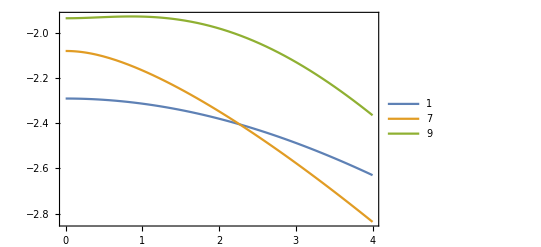

```mathematica
select = {1, 7, 9};
plStatesNoGamma = Plot[Evaluate[Table[hmeig[[select[[i]]]] /. Δ->1/2,{i,1,Length[select]}]],{Γ,0,4},PlotRange->All,Axes->{True,False},Frame->True,PlotStyle->Thick, PlotLegends->Evaluate[Table[ToString[select[[i]]],{i,1,Length[select]}]]]
```

```mathematica
plStates = 
Show[
Table[
Graphics3D[
{
MapIndexed[
Cases[#,Line[L_]:>{myPlotStyle[[i]][[1]],myPlotStyle[[i]][[2]],Line[Thread[{L[[All,1]],#2[[1]],L[[All,2]]}]]},-1]&,Table[Plot[hmeig[[select[[i]]]],{Γ,-4,4}],{Δ,-1,1,0.5}]
]
(* ,
MapIndexed[
Cases[#,Line[L_]:>{myPlotStyle[[i]][[1]],myPlotStyle[[i]][[2]],Line[Thread[{#2[[1]], L[[All,1]],L[[All,2]]}]]},-1]&,Table[Plot[hmeig[[select[[i]]]],{Γ,0,1}],{Δ,0,0,1}]
] *)
}
,Axes->True,Ticks->{Automatic,None,Automatic},AxesLabel->{"Γ/ζ","Δ/ζ","E"},BoxRatios->{1,1,1.5},PlotRange->All],
{i,1,Length[select]}]]
```

-Graphics3D-

For the state energies the sign of Delta matters, although the curves are qualitatively similar. Also the sign of Gamma doesn’t matter.

#### For completeness, print the model Hamiltonian in the basis of spinors:

```mathematica
hmsobas = Conjugate[soveco].hm.Transpose[soveco]//Simplify;
Print["Model Hamiltonian (CF + SO) in the basis of SO eigenfunctions, Angular momentum l = "<>ToString[l]];
tmp = hmsobas //TableForm[#, TableHeadings->{jmjlabels,jmjlabels},
TableSpacing->{1,1},TableAlignments->Right ]&
```

Model Hamiltonian (CF + SO) in the basis of SO eigenfunctions, Angular momentum l = 3

| |5/2,-5/2⟩ | |5/2,-3/2⟩ | |5/2,-1/2⟩ | |5/2,1/2⟩ | |5/2,3/2⟩ | |5/2,5/2⟩ | |7/2,-7/2⟩ | |7/2,-5/2⟩ | |7/2,-3/2⟩ | |7/2,-1/2⟩ | |7/2,1/2⟩ | |7/2,3/2⟩ | |7/2,5/2⟩ | |7/2,7/2⟩
|5/2,-5/2⟩ | -2+Δ/7 | 0 | 0 | 0 | 0 | 0 | 0 | -(√6 Δ)/7 | 0 | 0 | 0 | -Γ/(2 √2) | 0 | 0
|5/2,-3/2⟩ | 0 | -2+Δ/7 | 0 | 0 | 0 | 0 | 0 | 0 | (3 √10 Δ)/7 | 0 | 0 | 0 | 1/2 √(5/6) Γ | 0
|5/2,-1/2⟩ | 0 | 0 | -2+Δ/7 | 0 | 0 | 0 | 0 | 0 | 0 | -(10 √3 Δ)/7 | 0 | 0 | 0 | -1/2 √(5/21) Γ
|5/2,1/2⟩ | 0 | 0 | 0 | -2+Δ/7 | 0 | 0 | 1/2 √(5/21) Γ | 0 | 0 | 0 | (10 √3 Δ)/7 | 0 | 0 | 0
|5/2,3/2⟩ | 0 | 0 | 0 | 0 | -2+Δ/7 | 0 | 0 | -1/2 √(5/6) Γ | 0 | 0 | 0 | -(3 √10 Δ)/7 | 0 | 0
|5/2,5/2⟩ | 0 | 0 | 0 | 0 | 0 | -2+Δ/7 | 0 | 0 | Γ/(2 √2) | 0 | 0 | 0 | (√6 Δ)/7 | 0
|7/2,-7/2⟩ | 0 | 0 | 0 | 1/2 √(5/21) Γ | 0 | 0 | 3/2 | 0 | 0 | 0 | -1/4 √(5/7) Γ | 0 | 0 | 0
|7/2,-5/2⟩ | -(√6 Δ)/7 | 0 | 0 | 0 | -1/2 √(5/6) Γ | 0 | 0 | 3/2+(6 Δ)/7 | 0 | 0 | 0 | Γ/(4 √3) | 0 | 0
|7/2,-3/2⟩ | 0 | (3 √10 Δ)/7 | 0 | 0 | 0 | Γ/(2 √2) | 0 | 0 | 3/2-(8 Δ)/7 | 0 | 0 | 0 | Γ/(4 √3) | 0
|7/2,-1/2⟩ | 0 | 0 | -(10 √3 Δ)/7 | 0 | 0 | 0 | 0 | 0 | 0 | 3/2+(6 Δ)/7 | 0 | 0 | 0 | -1/4 √(5/7) Γ
|7/2,1/2⟩ | 0 | 0 | 0 | (10 √3 Δ)/7 | 0 | 0 | -1/4 √(5/7) Γ | 0 | 0 | 0 | 3/2+(6 Δ)/7 | 0 | 0 | 0
|7/2,3/2⟩ | -Γ/(2 √2) | 0 | 0 | 0 | -(3 √10 Δ)/7 | 0 | 0 | Γ/(4 √3) | 0 | 0 | 0 | 3/2-(8 Δ)/7 | 0 | 0
|7/2,5/2⟩ | 0 | 1/2 √(5/6) Γ | 0 | 0 | 0 | (√6 Δ)/7 | 0 | 0 | Γ/(4 √3) | 0 | 0 | 0 | 3/2+(6 Δ)/7 | 0
|7/2,7/2⟩ | 0 | 0 | -1/2 √(5/21) Γ | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 √(5/7) Γ | 0 | 0 | 0 | 3/2